```mathematica
Clear["Global`*"]
ClearAll["Global`*"]
Clear["Global`*"]
ClearAll[r,θ,ϕ,t,s]


ρ=r^2+a^2 Cos[θ]^2; 
Δ=r^2-2 m r+a^2;

(*Usual Boyer-Lindquist*)
metric=-{{-ρ/Δ,0,0,0},{0,-ρ,0,0},{0,0,-(((r^2+a^2)^2-Δ a Sin[θ]^2)/ρ) Sin[θ]^2,(a Sin[θ]^2( r^2 +a^2-Δ))/ρ},{0,0,(a Sin[θ]^2( r^2 +a^2-Δ))/ρ,(Δ-a^2 Sin[θ]^2)/ρ}};

inversemetric = Simplify[Inverse[metric]];
coord={r,θ,ϕ,t};
christ[i_,j_,k_]:=christ[i,j,k]=Simplify[Sum[1/2 inversemetric[[i,d]] (D[metric[[d,k]],coord[[j]]]+D[metric[[d,j]],coord[[k]]]-D[metric[[j,k]],coord[[d]]]),{d,1,4}]]
eq=Table[coord[[i]]''+Sum[christ[i,j,k] coord[[j]]' coord[[k]]',{j,1,4},{k,1,4}],{i,1,4,1}];
eqs=eq/. {r''->r''[s],θ''->θ''[s],ϕ''->ϕ''[s],t''->t''[s],r'->r'[s],θ'->θ'[s],ϕ'->ϕ'[s],t'->t'[s],r->r[s],θ->θ[s],ϕ->ϕ[s],t->t[s]};
```

```mathematica
initFromELQ[E0_,Lz0_,Q0_,r0_,th0_,pr_,pθ_,a0_,m0_]:=Module[{Delta,rho2,Rr,ThetaTh,dr,dr2,dth,dth2,dt,dph,det,sinth2,costh2,csc2,gtt,gtϕ,grr,gϕϕ,gθθ},

Delta=r0^2-2 m0 r0+a0^2;
rho2=r0^2+a0^2 Cos[th0]^2;
sinth2=Sin[th0]^2;
costh2=Cos[th0]^2;
csc2=1/sinth2;

{grr,gθθ,gϕϕ,gtϕ,gtt}={metric[[1,1]],metric[[2,2]],metric[[3,3]],metric[[3,4]],metric[[4,4]]} /. {r->r0,θ->th0,m->m0,a->a0};
det=gtϕ^2-gtt*gϕϕ;

dt=(gϕϕ*E0+gtϕ*Lz0)/det;
dph=(-gtϕ*E0-gtt*Lz0)/det;
dth2= Q0-costh2(a0^2(1-E0^2)+(Lz0^2 *csc2));
dth=Sqrt[dth2/gθθ];
(*dr2=-1-gtt*dt^2-2*gtϕ*dt*dph-gϕϕ*dph^2-gθθ*dth^2;
dr=-Sqrt[dr2/grr];*)
Rr=((r0^2+a0^2)*E0-a0*Lz0)^2-Delta*(Q0+(Lz0-a0*E0)^2+r0^2);
dr=-Rr/rho2^2;

(*dth=pθ/rho2;
dr=(Delta/rho2)pr;*)

{t[0]==0,r[0]==r0,θ[0]==th0,ϕ[0]==0,t'[0]==dt,r'[0]==dr,θ'[0]==dth,ϕ'[0]==dph}];



(*INIT CONDITIONS*)
E0=1;L0=4;Q=0.01;r0=40;th0=Pi/2;pr=0;pθ=1.9;a0=0.9;m0=1;

EQ=Table[eqs[[i]]==0/. {m->m0,a->a0},{i,1,4}];
Radius=2;
values ={};
sSingular=100;
phi=0.05;
```

```mathematica
aVariation[aVar_] :=Module[{kerr,initConds,U,U0,U1, rFunc,θFunc,ϕFunc, tFunc,primer,P2,sMax,rStar,sola1,a1,b1,F0,gtt0,newInit,Finalenergy},
(*First Calculate the geodesic for a given parameter*)
initConds= initFromELQ[E0,L0,Q,r0,th0,pr,pθ,aVar,m0];
kerr =NDSolve[{EQ, initConds
},
{r,θ,ϕ,t},
{s,0,sSingular},
Method->{"StiffnessSwitching"},MaxStepSize->0.01,
AccuracyGoal->1,PrecisionGoal->1
];

{rFunc,θFunc,ϕFunc, tFunc}={r,θ,ϕ,t}/. kerr[[1]];
U[s_] :={r'[s],θ'[s],ϕ'[s],t'[s]}/. kerr[[1]];
primer[s_]:=E0*U[s]-{0,0,0,1};  (*Kronecker delta:only t component gets-1*)
P2[s_] := metric[[4,4]]+E0^2 /. {r->rFunc[s],θ->θFunc[s], m->m0, a->aVar};
sMax=NArgMax[{P2[s],0.00001<s<100},s];
rStar={Sqrt[aVar^2+rFunc[sMax]^2] Sin[θFunc[sMax]] Cos[ϕFunc[sMax]],Sqrt[aVar^2+rFunc[sMax]^2] Sin[θFunc[sMax]] Sin[ϕFunc[sMax]],rFunc[sMax] Cos[θFunc[sMax]]};

U0=U[sMax];
gtt0 =metric[[4,4]] /.{r->rFunc[sMax],θ->θFunc[sMax], m->m0, a->aVar};

sola1=Solve[-a1^4*metric[[4,4]]+2a^3*metric[[4,4]]+a^2*metric[[4,4]]-1==0/.{r->rFunc[sMax],θ->θFunc[sMax], m->m0, a->a0},a1];
b1=gtt0*a1 ;
F0 = a1*{1,0,0,0}+b1*U0 /.sola1[[1]];

U1=Cosh[phi]*U0+Sinh[phi]*F0;
newInit={
r[sMax]==rFunc[sMax],θ[sMax]==θFunc[sMax],ϕ[sMax]==ϕFunc[sMax],t[sMax]==tFunc[sMax],
r'[sMax]==U1[[1]],θ'[sMax]==U1[[2]],ϕ'[sMax]==U1[[3]],t'[sMax]==U1[[4]]};
Finalenergy = (U1[[4]]*metric[[4,4]]+2*U1[[3]]*metric[[3,4]])/(U0[[4]]*metric[[4,4]]+2*U0[[3]]*metric[[3,4]]) /. {a->aVar, m->1,r->rFunc[sMax],θ->θFunc[sMax]};
{Finalenergy}];
aVariation[0.9]
```

{1.06497}

NDSolve::ndsz: At s == 0.906087, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {4.57319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {40.8288} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

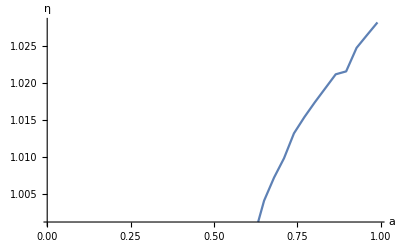

```mathematica
Plot[aVariation[a],{a,0.01,0.99},PlotPoints->5,PerformanceGoal->"Speed",AxesLabel->{"a","η"}]
```

```mathematica
aTrajectory[aVar_] :=Module[{kerr,initConds,U,U0,rFunc,θFunc,ϕFunc, tFunc,primer,P2,sMax,rStar,marker,trajectory},
(*First Calculate the geodesic for a given parameter*)
initConds= initFromELQ[E0,L0,Q,r0,th0,pr,pθ,aVar,m0];
kerr =NDSolve[{EQ, initConds
},
{r,θ,ϕ,t},
{s,0,sSingular},
Method->{"StiffnessSwitching"},MaxStepSize->0.01,
AccuracyGoal->10,PrecisionGoal->10
];

{rFunc,θFunc,ϕFunc, tFunc}={r,θ,ϕ,t}/. kerr[[1]];
U[s_] :={r'[s],θ'[s],ϕ'[s],t'[s]}/. kerr[[1]];
primer[s_]:=E0*U[s]-{0,0,0,1};  (*Kronecker delta:only t component gets-1*)
P2[s_] := metric[[4,4]]+E0^2 /. {r->rFunc[s],θ->θFunc[s], m->m0, a->aVar};
sMax=NArgMax[{P2[s],0.00001<s<100},s];
rStar={Sqrt[aVar^2+rFunc[sMax]^2] Sin[θFunc[sMax]] Cos[ϕFunc[sMax]],Sqrt[aVar^2+rFunc[sMax]^2] Sin[θFunc[sMax]] Sin[ϕFunc[sMax]],rFunc[sMax] Cos[θFunc[sMax]]};
marker=Graphics3D[{Red,Sphere[rStar,0.3]}];
trajectory=ParametricPlot3D[{Sqrt[aVar^2+rFunc[s]^2]*Sin[θFunc[s]]*Cos[ϕFunc[s]],Sqrt[aVar^2+rFunc[s]^2]*Sin[θFunc[s]]*Sin[ϕFunc[s]],rFunc[s]*Cos[θFunc[s]]},{s,0,100},ColorFunction->Hue,AxesLabel->{"x","y","z"},PerformanceGoal->"Quality",PlotRange->{{-15,15},{-15,15},{-15,15}},RegionFunction->Function[{x,y,z,s},Sqrt[x^2+y^2+z^2]>10^-8],Exclusions->None];
{trajectory,marker}];
```

```mathematica
Show[aTrajectory[0.9]]
```

-Graphics3D-

```mathematica
BlackHole[a_]:=ParametricPlot3D[
{
{a*Cos[φ],a*Sin[φ],0},
{(Sqrt[( m0+Sqrt[m0^2-a^2 Cos[θ]^2])^2+a^2] Sin[θ] Cos[φ]),(Sqrt[( m0+Sqrt[m0^2-a^2 Cos[θ]^2])^2+a^2] Sin[θ] Sin[φ]),(( m0+Sqrt[m0^2-a^2 Cos[θ]^2])Cos[θ])},(*Outer horizon*)
{(Sqrt[(m0-Sqrt[m0^2-a^2 Cos[θ]^2])^2+a^2] Sin[θ] Cos[φ]),(Sqrt[(m0-Sqrt[m0^2-a^2 Cos[θ]^2])^2+a^2] Sin[θ] Sin[φ]),((m0-Sqrt[m0^2-a^2 Cos[θ]^2])Cos[θ])},  (*Inner horizon*)
{(Sqrt[(m0+Sqrt[m0^2-a^2])^2+a^2] Sin[θ] Cos[φ]),(Sqrt[(m0+Sqrt[m0^2-a^2])^2+a^2] Sin[θ] Sin[φ]),((m0+Sqrt[m0^2-a^2]) *Cos[θ])},(*Outer horizon*)
{(Sqrt[(m0-Sqrt[m0^2-a^2])^2+a^2] Sin[θ] Cos[φ]),(Sqrt[(m0-Sqrt[m0^2-a^2])^2+a^2] Sin[θ] Sin[φ]),((m0-Sqrt[m0^2-a^2])*Cos[θ])}(*Inner horizon*)
},
{θ,0,Pi},{φ,0,2 Pi},PlotStyle->{
Directive[Red,Thickness[0.09]],
Directive[Green,Opacity[0.1]],(*Outer horizon*)
Directive[Blue,Opacity[0.3]] ,  (*Inner horizon*)
Directive[Gray,Opacity[0.2]],(*Outer horizon*)
Directive[Gray,Opacity[0.5]]    (*Inner horizon*)},
Mesh->None,
PerformanceGoal->"Quality", 
PlotRange->{{-5,5},{-5,5},{-5,5}}
] 
b=0.9;
Show[BlackHole[b],aTrajectory[b]]
```

-Graphics3D-

```mathematica
rSplus[θ_] := m0+Sqrt[m0^2-a0^2 Cos[θ]^2];
rSminus[θ_] := m0-Sqrt[m0^2-a0^2 Cos[θ]^2];
rHplus=m0+Sqrt[m0^2-a0^2];
rHminus=m0-Sqrt[m0^2-a0^2];

Manipulate[
ParametricPlot3D[
{
{a*Cos[φ],a*Sin[φ],0},
{(Sqrt[( m0+Sqrt[m0^2-a^2 Cos[θ]^2])^2+a^2] Sin[θ] Cos[φ]),(Sqrt[( m0+Sqrt[m0^2-a^2 Cos[θ]^2])^2+a^2] Sin[θ] Sin[φ]),(( m0+Sqrt[m0^2-a^2 Cos[θ]^2])Cos[θ])},(*Outer horizon*)
{(Sqrt[(m0-Sqrt[m0^2-a^2 Cos[θ]^2])^2+a^2] Sin[θ] Cos[φ]),(Sqrt[(m0-Sqrt[m0^2-a^2 Cos[θ]^2])^2+a^2] Sin[θ] Sin[φ]),((m0-Sqrt[m0^2-a^2 Cos[θ]^2])Cos[θ])},  (*Inner horizon*)
{(Sqrt[(m0+Sqrt[m0^2-a^2])^2+a^2] Sin[θ] Cos[φ]),(Sqrt[(m0+Sqrt[m0^2-a^2])^2+a^2] Sin[θ] Sin[φ]),((m0+Sqrt[m0^2-a^2]) *Cos[θ])},(*Outer horizon*)
{(Sqrt[(m0-Sqrt[m0^2-a^2])^2+a^2] Sin[θ] Cos[φ]),(Sqrt[(m0-Sqrt[m0^2-a^2])^2+a^2] Sin[θ] Sin[φ]),((m0-Sqrt[m0^2-a^2])*Cos[θ])}(*Inner horizon*)
},
{θ,0,Pi},{φ,0,2 Pi},PlotStyle->{
Directive[Red,Thickness[0.09]],
Directive[Green,Opacity[0.1]],(*Outer horizon*)
Directive[Blue,Opacity[0.3]] ,  (*Inner horizon*)
Directive[Gray,Opacity[0.2]],(*Outer horizon*)
Directive[Gray,Opacity[0.5]]    (*Inner horizon*)},
Mesh->None,
PerformanceGoal->"Quality", 
PlotRange->{{-5,5},{-5,5},{-5,5}}
],
{{a,1,"a"},0,1},
{{m0,1,"m"},0,1}
]
```